```mathematica
f0=Pi/6;
Φ[σ_,  μ1_, μ2_, Y1_, Y2_]:= 2 r + σ(μ1 Abs[r - Y1]- μ2 Abs[r + Y2] ); 
labels = {"-", "+", "++","-+","--","+-"};
labels =Join[labels,{"--+", "+--", "++-","-+-","---","-++","+-+","+++"}];
```

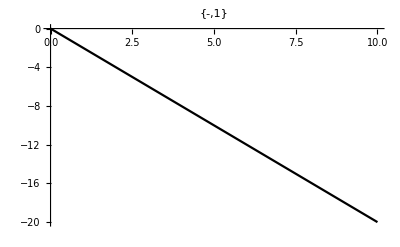
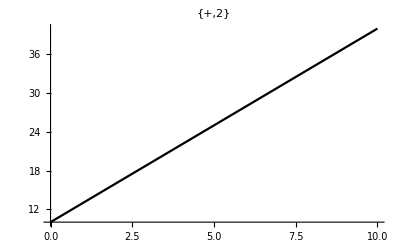
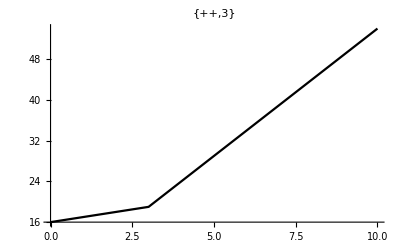
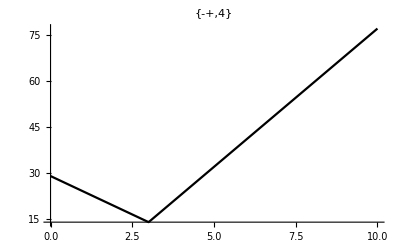
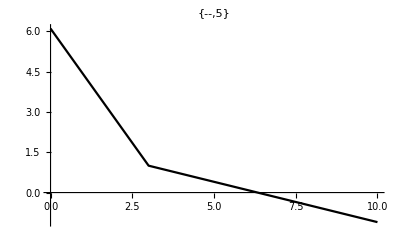
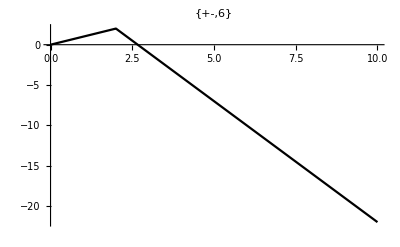

```mathematica
F[1] = Φ[ 1,0,0,3,2];
F[2] = Φ[ 1,0,5,3,2];
F[3] = Φ[1,-2,5,3,2];
F[4] = Φ[1,-7,4,3,2];
F[5] = Φ[1,-0.7,1,3,4];
F[6] = Φ[1,2,1,2,4];
Table[Plot[- F[i],{r,0,10},PlotLabel->{labels[[i]] , i},PlotRange->All,PlotStyle->Black],{i, 1,6}]
```

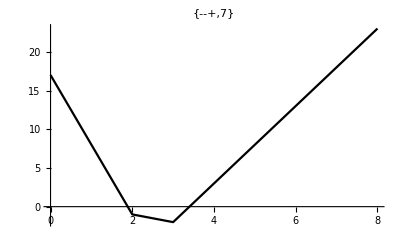
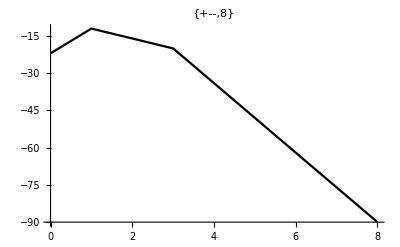
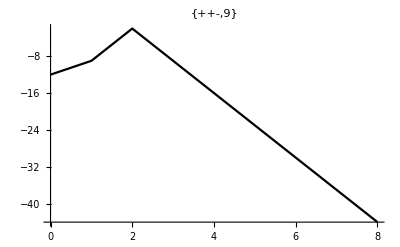
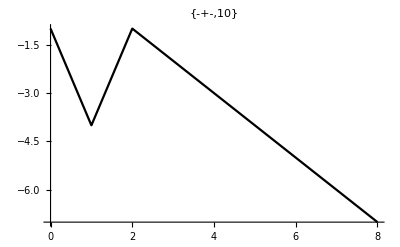
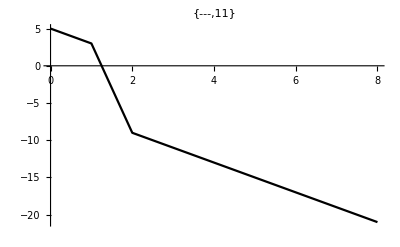
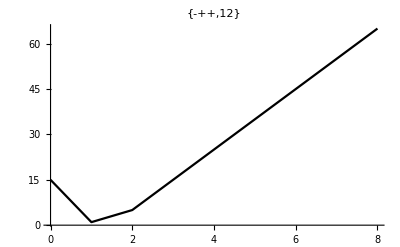

```mathematica
F[7] = Φ[1,-3,4,3,-2];
F[8] = Φ[1,5,-7,3,-1];
F[9] = Φ[1,-2,-7,1,-2];
F[10] = Φ[1,2,3,2,-1];
F[11] = Φ[1,-5,-5,2,-1];
F[12] = Φ[1, -3,9,2,-1];
Table[Plot[- F[i],{r,0, 8},PlotLabel->{labels[[i]] , i},PlotRange->All,PlotStyle->Black],{i, 7,12}]
```